## Solution CP-3: Solving ordinary differential equations (ODEs)

§5 of the Mathematica tutorial shows how Mathematica can be used to analyze an ordinary differential equation (ODE). Here we illustrate this material by means of a familiar example, the kinetics of a drug that is supplied continuously by infusion.

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

### Introduction: Solving and analyzing differential equations with Mathematica

We consider the ODE describing the kinetics of a drug that is continuously supplied by infusion. The ODE is given by: ⅆm/ⅆt=f(m)=1/B(α-β·m)
m(t) = concentration of medicine in blood (mg/liter), 
B = total amount of blood (in liters), 
α = infusion rate (mg/min), 
β = amount of blood being purged in the kidneys (liters/hour).

Work systematically through the following sections of the notebook by executing the commands one by one:

#### Quantitative analysis I: Analytical solution of an ODE

The ODE can be entered as follows:

```mathematica
ode=D[m[t],t]==(1/B)*(alpha-beta*m[t])
```

m'[t]==(alpha-beta m[t])/B

First, we derive the general solution of the ODE. To do this, we use the DSolveValue[ode, expr, var] command:

```mathematica
solGen=DSolveValue[ode,m[t],t]
```

alpha/beta+ⅇ^(-(beta t)/B) C[1]

Although the ODE contains a number of unspecified parameters (B, α, β), Mathematica has no problem to find the general solution. This solution still contains the arbitrary constant C[1]. In general, we recommend to specify some general initial conditions like m(0)=m_0, since Mathematica then gives the solution in a more useful form, showing directly how the solution depends on the initial conditions. To this end, the command DSolveValue[{ode, init}, expr, var] should be used:

```mathematica
init=m[0]==m0;
solSpec=DSolveValue[{ode,init},m[t],t]
```

(ⅇ^(-(beta t)/B) (-alpha+alpha ⅇ^((beta t)/B)+beta m0))/beta

We are usually interested in the special case that m(0)=0, i.e. the case that there is no drug in the bloodstream at the moment the infusion starts. This can be either done by specifying m0=0 or with the help of the substitute command:

```mathematica
sol0=DSolveValue[{ode,init/.m0->0},m[t],t]
```

(alpha ⅇ^(-(beta t)/B) (-1+ⅇ^((beta t)/B)))/beta

In practice, we often want to get quantitative information about the process that is modelled by the ODE. For example, we might want to know the concentration of the drug in the bloodstream after 24 hours or the concentration ultimately reached after a long period of time. We also might wish to plot the concentration as a function of time. For all this, we first have to specify the parameters α, β and B in the ODE, e.g. α=0.6, β=0.3, B=5. Then the solution is given by:

```mathematica
alpha=0.6;
beta=0.3;
B=5;
sol0
```

2. ⅇ^(-0.06 t) (-1+ⅇ^(0.06 t))

Let us first plot the solution for 100 timesteps:

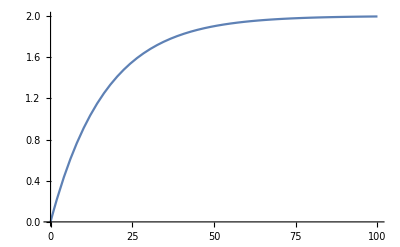

```mathematica
Plot[sol0,{t,0,100}]
```

From the graph, we see that the concentration converges asymptotically to the value 2 mg/liter, and that after 24 hours the concentration is approximately 1.5 mg/liter. We can confirm this by direct calculation:

```mathematica
sol0/.t->24
Limit[sol0,t->Infinity]
```

1.52614

2.

#### Quantitative analysis II: Numerical solution of an ODE

The ODE in our example is simple enough to be solvable analytically. Unfortunately, even simple-looking ODEs do often not have a ‘nice’ analytical solution. Fortunately, Mathematica is able to calculate an approximate solution even for such cases. Such a ‘numeric solution’ is obtained by using the ‘numeric’ version of the command: NDSolveValue[]. As explained in §5.2 of the Mathematica Tutorial, this only works if all parameters have been assigned numerical values. Let us restart, enter the ODE, specify all parameters and calculate the numerical solution of our ODE:

```mathematica
Quit[]
```

```mathematica
ode=D[m[t],t]==(1/B)*(alpha-beta*m[t]);
init=m[0]==m0;
alpha=0.6;
beta=0.3;
B=5;
solNum=NDSolveValue[{ode,init/.m0->0},m[t],{t,0,100}]
```

InterpolatingFunction[{{0., 100.}}, <>][t]

The output is not very rewarding and recognizable, but you can in fact plot a graph of it:

```mathematica
Plot[solNum,{t,0,100}]
```

-Graphics-

As you see, the graph of the numerical solution is virtually identical to that of the analytical solution produced above. We can still obtain numerical values, e.g. the concentration of the drug after 24 hours:

```mathematica
solNum/.t->24
```

1.52614

Let us now check whether we can also use the numerical solution for obtaining the limit concentration after a long period of time:

```mathematica
Limit[solNum,t->Infinity]
```

Limit[InterpolatingFunction[{{0., 100.}}, <>][t],t→∞]

This does not work. The reason is simple: the numerical solution can only be obtained for a finite time interval (in this case [0,100]). Mathematica cannot say anything about the asymptotic values for t -> ∞.

#### Qualitative analysis: Equilibrium and stability analysis

Let us now perform a qualitative analysis of the ODE, i.e. let us calculate the equilibria and determine their stability. Since we want to do this in full generality, we first have to unassign all the parameters (which have given specific values in the previous section).:

```mathematica
Clear[alpha,beta,B]
```

The qualitative analysis of an autonomous ODE ⅆz/ⅆt=f(z) is based on the investigation of the function f that specifies the right-hand side of the ODE. At an equilibrium, the system does not change any more or, equivalently, ⅆz/ⅆt=0. Hence equilibria are determined by the equilibrium equation f(z^*)=0. To determine the stability of an equilibrium, we take the derivative of f and fill in the equilibrium z^*. If  f'(z^*)<0 (stability criterion), the equilibrium is stable; if  f'(z^*)>0 the equilibrium is unstable. We start the qualitative analysis by giving the right-hand side of our ODE a name:

```mathematica
f=(1/B)*(alpha-beta*m)
```

(alpha-beta m)/B

Note that we define f as a function of m, and not of m(t). We use the Solve[] command to determine the equilibria with the help of the equilibrium equation. Then we calculate the derivative of f with the help of D[], we substitute the equilibrium into this derivative, and we store the result in the variable stabCrit. If this stability criterion is negative, the equilibrium is stable, if it is positive, the equilibrium is unstable. Here we get:

```mathematica
eq=Values[Solve[f==0,m]]
stabCrit=D[f,m]/.m->eq
```

{{alpha/beta}}

-beta/B

Hence our ODE has exactly one equilibrium (at m^*=α/β), and this equilibrium is stable since stabCrit is negative. Let us now apply this to our standard parameter values (α=0.6, β=0.3, B=5). Let us first assign a name to this parameter combination, then plot the function f and calculate the specific value of the equilibrium:

1/5 (0.6-0.3 m)

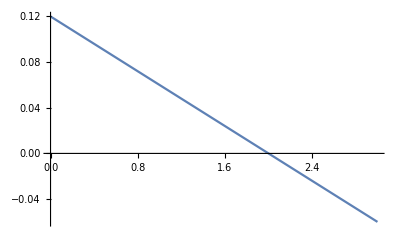

{{2.}}

-0.06

stable

```mathematica
param={alpha->0.6,beta->0.3,B->5};
f1=f/.param
Plot[f1,{m,0,3}]
eq1=eq/.param
stabCrit1=stabCrit/.param
If[stabCrit1<0,"stable","unstable"]
```

The last command line returns ‘stable’ if the stability criterion is negative and ‘not stable’ otherwise. A qualitative analysis is often performed instead of a quantitative analysis, for example because the ODE is not analytically solvable. If, as in our case, the ODE is solvable, we can specify the ODE directly with f, i.e. without having to retype a command:

```mathematica
ode=D[m[t],t]==(f/.m->m[t])
```

m'[t]==(alpha-beta m[t])/B

(ⅇ^(-(beta t)/B) (-alpha+alpha ⅇ^((beta t)/B)+beta m0))/beta

3.33333 ⅇ^(-0.06 t) (-0.6+0.6 ⅇ^(0.06 t)+0.3 m0)

2.

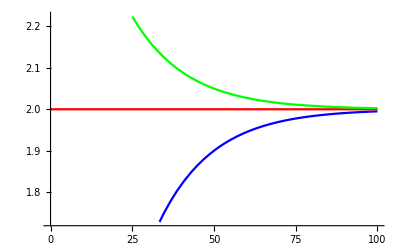

```mathematica
sol=DSolveValue[{ode,m[0]==m0},m[t],t]
sol1=sol/.param
Limit[sol1,t->Infinity]
Plot[{sol1/.m0->0,sol1/.m0->eq1,sol1/.m0->3},{t,0,100},PlotStyle->{Blue,Red,Green}]
```

We see that, indeed, the solution curves converge to the stable equilbrium m^*=α/β=0.6/0.3=2.

### Exercise 3-1: From the pen&paper practical.........

Solve the following differential equations from the pen & paper practical for initial values z_0=1 and z_0=0. If Mathematica does not match the solution in the Workbook: try to explain why not.

#### (a) ⅆz/ⅆt=(3 t^2)/z

```mathematica
ode=D[z[t],t]==(3*t^2)/z[t]
z0=1;
DSolveValue[{ode,z[0]==z0},z[t],t]
z0=0;
DSolveValue[{ode,z[0]==z0},z[t],t]
```

z'[t]==(3 t^2)/z[t]

DSolveValue::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

√(1+2 t^3)

DSolveValue::dsvb: There are multiple solution branches for the equations, but DSolveValue will return only one. Use DSolve to get all of the solution branches.

-√2 √(t^3)

#### (b) ⅆz/ⅆt=3 zt^2

```mathematica
ode=D[z[t],t]==(3*z[t]*t^2)
z0=1;
DSolveValue[{ode,z[0]==z0},z[t],t]
z0=0;
DSolveValue[{ode,z[0]==z0},z[t],t]
```

z'[t]==3 t^2 z[t]

ⅇ^(t^3)

0

#### (c) ⅆz/ⅆt=3 t^2

```mathematica
ode=D[z[t],t]==(3*t^2)
z0=1;
DSolveValue[{ode,z[0]==z0},z[t],t]
z0=0;
DSolveValue[{ode,z[0]==z0},z[t],t]
```

z'[t]==3 t^2

1+t^3

t^3

#### (d) ⅆz/ⅆt=3 z^2

```mathematica
ode=D[z[t],t]==(3*z[t]^2)
z0=1;
DSolveValue[{ode,z[0]==z0},z[t],t]
z0=0;
DSolveValue[{ode,z[0]==z0},z[t],t]
```

z'[t]==3 z[t]^2

1/(1-3 t)

DSolveValue::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

DSolveValue[{z'[t]==3 z[t]^2,z[0]==0},z[t],t]

#### (e) ⅆz/ⅆt=2z·(3t-2)

```mathematica
ode=D[z[t],t]==2*z[t]*(3*t-2)
z0=1;
DSolveValue[{ode,z[0]==z0},z[t],t]
z0=0;
DSolveValue[{ode,z[0]==z0},z[t],t]
```

z'[t]==2 (-2+3 t) z[t]

ⅇ^(-4 t+3 t^2)

0

#### (f) ⅆz/ⅆt=2t·(3z-2)

```mathematica
ode=D[z[t],t]==2*t*(3*z[t]-2)
z0=1;
DSolveValue[{ode,z[0]==z0},z[t],t]
z0=0;
DSolveValue[{ode,z[0]==z0},z[t],t]
```

z'[t]==2 t (-2+3 z[t])

1/3 (2+ⅇ^(3 t^2))

-2/3 (-1+ⅇ^(3 t^2))

#### (g) ⅆ/ⅆt=2t·(3t-2)

```mathematica
ode=D[z[t],t]==2*t*(3*t-2)
z0=1;
DSolveValue[{ode,z[0]==z0},z[t],t]
z0=0;
DSolveValue[{ode,z[0]==z0},z[t],t]
```

z'[t]==2 t (-2+3 t)

1-2 t^2+2 t^3

2 (-t^2+t^3)

#### (h) ⅆz/ⅆt=2z·(3z-2)

```mathematica
ode=D[z[t],t]==2*z[t]*(3*z[t]-2)
z0=1;
DSolveValue[{ode,z[0]==z0},z[t],t]
z0=0;
DSolveValue[{ode,z[0]==z0},z[t],t]
```

z'[t]==2 z[t] (-2+3 z[t])

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-2/(-3+ⅇ^(4 t))

DSolveValue::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

DSolveValue[{z'[t]==2 z[t] (-2+3 z[t]),z[0]==0},z[t],t]

### Exercise 3-2: Seasonal effects on reproduction

Many populations grow during the summer months and decline during the winter. In other words, the per capita growth rate is oscillating around zero. The function 1/N ⅆN/ⅆt=g(N,t)=r·cos(2πt) can be used to model such a situation. The corresponding differential equation (ODE) is non-autonomous and given by ⅆN/ⅆt=N·g(N,t)=r·N·cos(2πt).
(a) Solve this ODE with Mathematica for N(0)=N_0.
(b) Plot this ODE for r=2 and N_0=50, for 0<t<3.

```mathematica
Quit[]
```

Before we start, let us first plot the function g(N,t) for the special case  r=2:

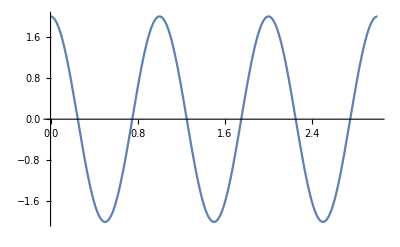

```mathematica
Plot[2*Cos[2*Pi*t],{t,0,3}]
```

```mathematica
f=r*n[t]*Cos[2*Pi*t]
eq=Values[Solve[f==0,n]]
ode=D[n[t],t]==f
solGen=DSolveValue[ode,n[t],t]
init=n[0]==n0
solSpec=DSolveValue[{ode,init},n[t],t]
```

r Cos[2 π t] n[t]

{}

n'[t]==r Cos[2 π t] n[t]

ⅇ^((r Sin[2 π t])/(2 π)) C[1]

n[0]==n0

ⅇ^((r Sin[2 π t])/(2 π)) n0

Here we are interested in the special case r=2 and N_0=50:

```mathematica
sol50=solSpec/.{r->2,n0->50}
```

50 ⅇ^(Sin[2 π t]/π)

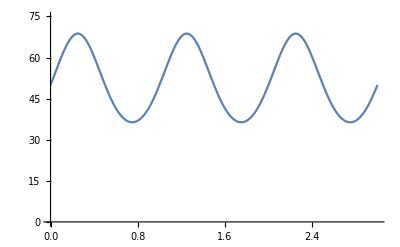

```mathematica
Plot[sol50,{t,0,3},PlotRange->{0,75}]
```

Not unexpectedly, the population density starts at N_0=50 and fluctuates between two extreme values. These values can easily be calculated:

```mathematica
nMax=sol50/.t->0.25
nMin=sol50/.t->0.75
```

68.7401

36.3689

Alternatively, you could solve the ODE numerically and plot the result. This is only possible if all parameters and intial conditions are fully specified:

```mathematica
r=2;
n0=50;
solNum=NDSolveValue[{ode,init},n[t],{t,0,3}]
Plot[solNum,{t,0,3},PlotRange->{0,75}]
```

InterpolatingFunction[{{0., 3.}}, <>][t]

-Graphics-

### Exercise 3.3: Exponential and logistic growth

The logistic growth equation is given by ⅆN/ⅆt=r·N·(1-N/K).  For small population densities N, the solution of the logistic growth equation is almost identical to the solution of the ODE for exponential growth ⅆN/ⅆt=r·N.
(a) Solve both ODEs with Mathematica in general, and specifically for N(0)=N_0.
(b) Plot both ODEs in one graph for r=0.1, K=100 and N_0=0.1.

```mathematica
Quit[]
```

First we define the two ODEs and calculate both the general and the specific solution:

```mathematica
odeExp=D[n[t],t]==r*n[t]
solGenExp=DSolveValue[odeExp,n[t],t]
init=n[0]==n0;
solSpecExp=DSolveValue[{odeExp,init},n[t],t]
```

n'[t]==r n[t]

ⅇ^(r t) C[1]

ⅇ^(r t) n0

```mathematica
odeLog=D[n[t],t]==r*n[t]*(1-n[t]/k)
solGenLog=DSolveValue[odeLog,n[t],t]
init=n[0]==n0;
solSpecLog=DSolveValue[{odeLog,init},n[t],t]
```

n'[t]==r n[t] (1-n[t]/k)

(ⅇ^(r t+k C[1]) k)/(-1+ⅇ^(r t+k C[1]))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(ⅇ^(r t) k n0)/(k-n0+ⅇ^(r t) n0)

To produce plots, we first have to specify all parameters:

{r→0.1,k→100,n0→0.1}

0.1 ⅇ^(0.1 t)

(10. ⅇ^(0.1 t))/(99.9+0.1 ⅇ^(0.1 t))

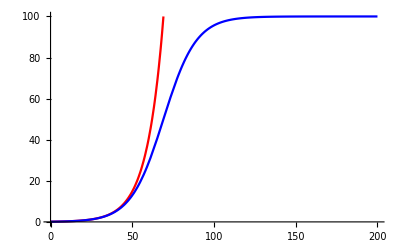

```mathematica
param={r->0.1,k->100,n0->0.1}
solSpecExp=solSpecExp/.param
solSpecLog=solSpecLog/.param
plotExp=Plot[{solSpecExp,solSpecLog},{t,0,200},PlotRange->{0,100},PlotStyle->{Red,Blue}]
```

(c) Analyze the logistic growth equation for equilibrium values by plotting graphs for a number of N_0: N_0=0,0.2,0.4,0.6,0.8,1

```mathematica
Quit[]
```

First,we plot the graph of f(N) to get an idea of, e.g., the zeroes of f(N):

n (1-n/k) r

{r→1,k→2}

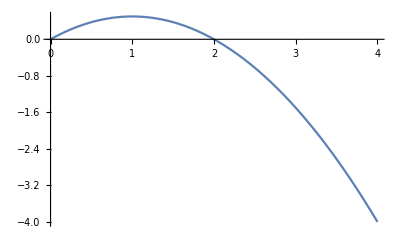

```mathematica
f[n_]=r*n*(1-n/k)
param={r->1,k->2}
Plot[f[n]/.param,{n,0,4}]
```

Next we solve the ODE ⅆN/ⅆt=f(N):

n'[t]==r n[t] (1-n[t]/k)

(ⅇ^(r t+k C[1]) k)/(-1+ⅇ^(r t+k C[1]))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(ⅇ^(r t) k n0)/(k-n0+ⅇ^(r t) n0)

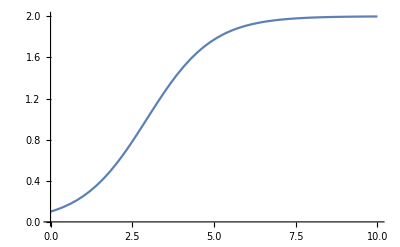

```mathematica
ode=D[n[t],t]==f[n[t]]
solGen=DSolveValue[ode,n[t],t]
init=n[0]==n0;
solSpec=DSolveValue[{ode,init},n[t],t]
sol=solSpec/.param;
Plot[sol/.n0->0.1,{t,0,10}]
```

Finally, we plot the solution for all values N_0=0,0.2,0.4,0.6,0.8,1 in one graph:

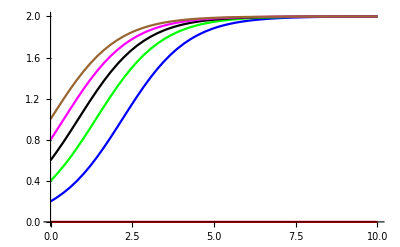

```mathematica
Plot[{sol/.n0->0,sol/.n0->0.2,sol/.n0->0.4,sol/.n0->0.6,sol/.n0->0.8,sol/.n0->1},{t,0,10},PlotStyle->{Red,Blue,Green,Black,Magenta,Brown}]
```

Nstar=2 seems to be a stable equilibrium point, and Nstar=0 seems to be an unstable equilibrium point. To verify this finding:

```mathematica
Nstar=Values[Solve[f[n]==0,n]]/.param
```

{{0},{2}}

```mathematica
f[Nstar[[1]]]/.param
f'[Nstar[[1]]]/.param
```

{0}

{1}

The function f(N) has a zero at N = Nstar[1] = 0, and the derivative of f(N) at N = Nstar[1] = 0  is positive. Hence Nstar[1] = 0 is an unstable equilibrium point.

```mathematica
f[Nstar[[2]]]/.param
f'[Nstar[[2]]]/.param
```

{0}

{-1}

The function f(N) has a zero at N = Nstar[2] = 0, and the derivative of f(N) at N = Nstar[2] = 0  is negative. Hence Nstar[2] = 0 is an stable equilibrium point.